```mathematica
SOI=Import["/users/pp/github/context/Mathematica/SOIM/data/soi.txt", "table"];
TSID=Import["/users/pp/github/context/Mathematica/SOIM/data/tsi.txt", "table"];
QBO=Import["/users/pp/github/context/Mathematica/SOIM/data/qbo20.txt", "table"];
QBO70=Import["/users/pp/github/context/Mathematica/SOIM/data/qbo.txt", "table"];
CW=Import["/users/pp/github/context/Mathematica/SOIM/data/cw.txt", "table"];
CW1=Import["/users/pp/github/context/Mathematica/SOIM/data/cw1_1930.txt", "table"];
CW0=Import["/users/pp/github/context/Mathematica/SOIM/data/cw1.txt", "table"];
NINO34=Import["/users/pp/github/context/Mathematica/SOIM/data/nino34ke.txt", "table"];
tahiti=Import["/users/pp/github/context/Mathematica/SOIM/data/tahiti.txt", "table"];
darwin=Import["/users/pp/github/context/Mathematica/SOIM/data/darwin0.txt", "table"];
noi=Import["/users/pp/github/context/Mathematica/SOIM/data/noi.txt", "table"];
```

{0.,0.434074}

-0.0528672

0.768228  = Correlation Coefficient

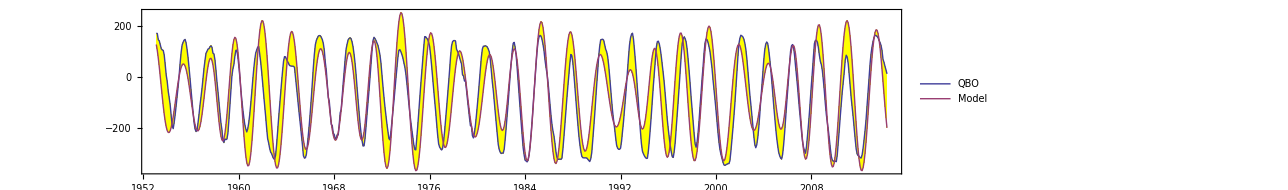

```mathematica
(* Data *)
MONTHS = 61.25;
Q = MeanFilter[QBO[[All,2]],4];  
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*MONTHS+1, 1}];        
(* Empirical Model fit *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
OSC := 9.305;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.036*Cos[2*Pi*x/(SEMI)+0.45]-0.17*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 
                     0.071*Cos[2*Pi*x/(CWR)+2.0]];
QBOfit[x_] :=(1.3*QBOG[x+0.0889]+1.2*QTO[x+0.0889])+1.16*CWG[x-0.04]+0.58*Diurnal[x+2.1]+1.23*Semidiurnal[x+0.6] ;
QBOshift[x_] := QBOfit[x-0.455] ;
QBOM = Table[{1953.0+x, -34.17*QBOshift[73.0+x]-72.4},{x,1/12,MONTHS+1/12, 1/12}];  

SDIF = QBOT[[All,2]]-QBOM[[All,2]];  
Variance[QBOT]-Variance[QBOM]
Mean[SDIF]
Correlation[QBOT,QBOM][[2,2]]  " = Correlation Coefficient"
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}, AspectRatio->0.1]
```

{7.24073 = char t,0.0648037 =err,1881.  .. ,1913.33,CC,14.0394,92.9234,78.8841}

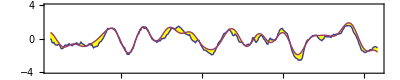

```mathematica
STRT=12; STRTY=1880+STRT/12; LNGTH=400; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.753;  TR=52.0;  SHFT=0.63;
RHS[x_] := 2.2*QBOshift[x+0.435];
SOLN=NDSolve[{y''[x]+0.753*y[x] == RHS[x], y'[TR]==-0.03, y[TR]==0.32}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.8*(-0.109*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x,-0*13 +STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{-0.0559509 =err, 1953 .. 2013 ,CC,88.175,88.175,0.}

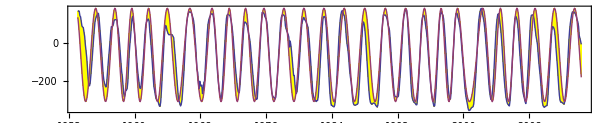

```mathematica
(* 234.320138688348*sin(1.47908160811451*cos(2.667874651*year + sin(2.56185156975765 + sin(0.2056357009*year) - sin(0.1697012411*year + sin(0.2056357009*year)*sin(0.0652446035803808*year)) - 0.365511588088449*year))) - 84.5168690958165 *)
(* Data *)
YEARS = 61.25;
Q = MeanFilter[QBO[[All,2]],3];  
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*MONTHS+1, 1}];        
(* Empirical Model fit *)
QBOyear[x_] :=  -( 1.47908160811451*Cos[2.667874651*x + Sin[2.56185156975765 + Sin[0.2056357009*x] - 
        Sin[0.1697012411*x + Sin[0.2056357009*x]*Sin[0.0652446035803808*x]] - 0.365511588088449*x]]);
QBOfit[x_] := QBOyear[x+1880.0-0.16];
QBOshift[x_] := QBOfit[x*1.00011] ;
QBOM = Table[{1953.0+x, (-200*QBOshift[73.0+x]-72.4)/1.2},{x,1/12,YEARS+1/12, 1/12}];  

SDIF = QBOT[[All,2]]-QBOM[[All,2]];  
OldCC = NewCC; NewCC = 100*Correlation[QBOT,QBOM][[2,2]];  
Var = Variance[SOIT]-Variance[SOIM];
Print[{ "=err" Var[[2]]," 1953 .. 2013 ","CC",OldCC,NewCC,NewCC-OldCC}]

ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, 
             Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}, AspectRatio->0.1]
```

{7.33885 = char t,-0.0559509 =err,1881.  .. ,1980.,CC,24.9835,61.0357,36.0522}

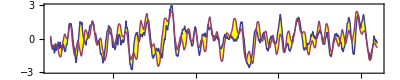

```mathematica
STRT=12; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 7;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.733;  TR=52.0;  SHFT=1.1;
DIU := 18.61;   CWR := 6.4827;  SEMI := 8.85; 
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Diurnal[x_] := -1.49*(0.06*Cos[2*Pi/(DIU/2)*x+3.6] -0.2*Cos[2*Pi/(DIU)*x+2.1] );
Semidiurnal[x_] := 0.15*Cos[2*Pi*x/(SEMI)+0.1]-0.5*Cos[2*Pi*x/(SEMI/2)+0.1];
Others[x_]:= + 2.5*CWG[x-0.4]+1.6*Diurnal[x+2.0]+0.8*Semidiurnal[x-0.4]+0.34*Cos[2*Pi/18.06*x-1.0];  (* RHS[x_] :=(1.25*QBOG[x+0.088]+1.4*CWG[x+0.08]+0.51*Diurnal[x+2.5]+0.9*Semidiurnal[x+0.5] ; *)
RHS[x_] := (-1.8*QBOfit'[x+0.11] + (1.1*QBOfit[x+0.1]) + 1.1*Others[x] - 0.2*Cos[2*Pi/46.0*x+0.6]+0*1*Cos[2*Pi/2.9*x+0.5])*(1+0.2*Cos[2*Pi/10.6*x+0.8]) -
           0.0*Cos[2*Pi*x-2.5];
SOLN=NDSolve[{y''[x]+CF*y[x] == 1.3*RHS[x-0.01], y'[TR]==-1.4, y[TR]==0.3}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.5*(0.0*RHS[x+SHFT]-First[y[1.001*x-0.06*Cos[2*Pi*x-0.5]-0.32*Sin[2*Pi/18.6*x-0.6]+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},   PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

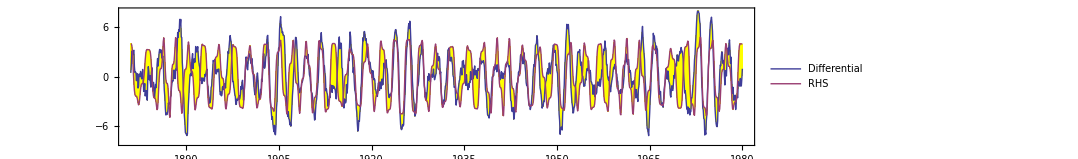

{7.33885 = char t,0.167613 =err,1881.  .. ,1980.,CC,37.9463,37.9463,0.}

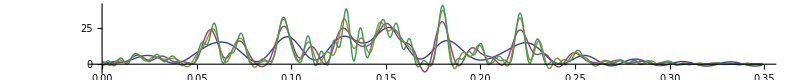

```mathematica
Window = 6; 
RHS[x_] := -1.5*QBOfit'[x] + 1.6*QBOfit[x];
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-0.733*R[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  -If[x>116.4,-1,1]*RHS[x*1.0012-0.16*Cos[2*Pi*x-0.6]-1.29]/1.55},{x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},    
              PlotLegends->{"Differential","RHS"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
```

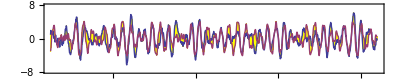

{7.33885 = char t,0.102423 =err,1881.  .. ,1980.,CC,62.6437,62.6437,1.42109×10^-14}

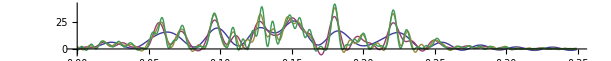

2.90888

```mathematica
Window = 7; 
STRT=12; LNGTH=1200;
(* STRT=220; LNGTH=300; *)
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-0.733*R[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
RHS[x_]:= Cos[2*Pi/2.3334*x-0.5*Cos[2*Pi*x-0.45]+0.4*Cos[2*Pi/18.63*x+0.8]-1.39]-
          0.8*Cos[2*Pi/2.909*x+1.0];
rhs=Table[{1880.0+x,  -2.3*If[x>100.3 && x<122.5,-1,1]*RHS[x]},    {x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},    
              PlotLegends->{"Differential","RHS"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
2*Pi/.18/12
```

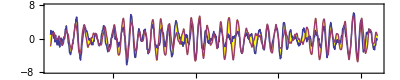

{7.35895 = char t,-1.4216 =err,1881.  .. ,1980.,CC,67.89,67.89,0.}

{7.35895 = char t,-0.188383 =err,1881.  .. ,1980.,CC,59.059,59.059,0.}

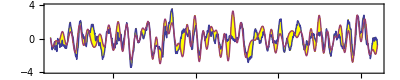

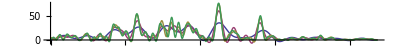

7.27221

```mathematica
Window = 7; 
STRT=12; LNGTH=1200;
(* STRT=220; LNGTH=300; *)
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-0.7333*R[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
qbo[x_]:= 1.13*Cos[2*Pi/2.3333*x-0.23*Cos[2*Pi*x-0.4]+0.5*Cos[2*Pi/18.63*x+0.9]-1.41]+ 0.55*Cos[2*Pi/2.239*x+0.1];  (* 0.99 *)
RHS[x_]:= qbo[x] -   1.1*Cos[2*Pi/2.905*x+0.6] ;  (* 0.99 *)
       (* 0.32*Cos[2*Pi/2.94*x+1.95]; *) (* 0.99 *)
rhs=Table[{1880.0+x,  -2.1*If[x>100.3 && x<116.4,-1,1]*RHS[x-0.01]},    {x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},    
              PlotLegends->{"Differential","RHS"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
(* Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1] *)
R = (1*MeanFilter[darwin[[All,2]],4])-(1*MeanFilter[tahiti[[All,2]],4]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.729;  TR=52.0;  SHFT=-1.2;
OSC := 9.305;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.12*Cos[2*Pi/OSC*x+3.5] +0.03*Cos[2*Pi/(2*OSC)*x+2.9]  );
Semidiurnal[x_] := 0.1*Cos[2*Pi*x/(SEMI)-1.3]-0*0.8*Cos[2*Pi*x/(SEMI/2)+0.1];
Tides[x_] := +1.1*Diurnal[x] + 0.4*Semidiurnal[x];
SOLN=NDSolve[{y''[x]+CF*y[x] == 8.9*RHS[x+0.17] + 0.25*Cos[2*Pi/6.52*x+0.1] +1.0*Tides[x], 
                               y'[TR]==3.7, y[TR]==0.0}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.6*(1.5*Cos[2*Pi/2.905*x+2.2]+First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIM[[All,2]]-SOIT[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.072/12
```

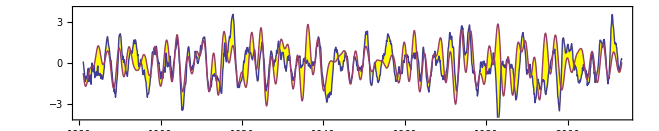

-Graphics-

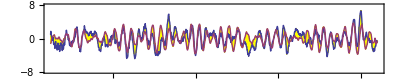

{4.03898 = char t,0.771058 =err,1881.  .. ,1980.,CC,53.756,53.79,0.0339987}

{4.03898 = char t,-0.0318643 =err,1881.  .. ,1980.,CC,68.8162,68.786,-0.0302055}

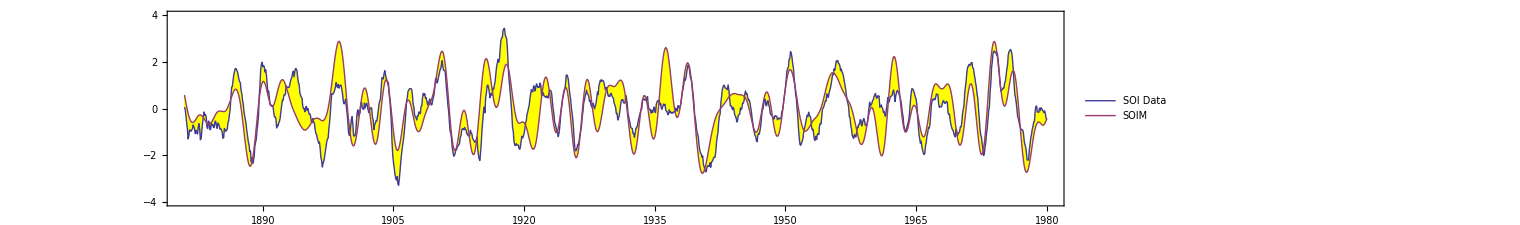

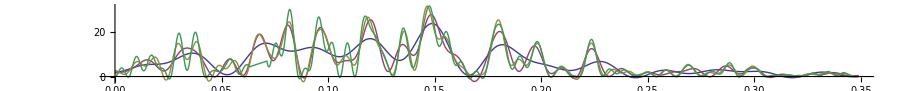

2.90888

```mathematica
Window = 7; 
STRT=12; LNGTH=1200;  CF = 2.42;
(* STRT=220; LNGTH=300; *)
R = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-CF*R[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
qbo[x_]:= 1.13*Cos[2*Pi/2.3333*x-0.23*Cos[2*Pi*x-0.4]+0.5*Cos[2*Pi/18.63*x+1.4]-1.4]+ 0.53*Cos[2*Pi/2.239*x+0.3];  (* 0.99 *)
RHS[x_]:= qbo[x] -   0.91*Cos[2*Pi/2.902*x+0.4] ;  (* 0.99 *)
       (* 0.32*Cos[2*Pi/2.94*x+1.95]; *) (* 0.99 *)
rhs=Table[{1880.0+x,  -1.5*If[x>99.3 && x<121,-1,1]*RHS[x-0.01]},    {x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,rhs},PlotRange->{-8,8},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},    
              PlotLegends->{"Differential","RHS"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
SDIF = lhs[[All,2]]-rhs[[All,2]];  
(* Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1] *)
Window := 5;
R = (1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
  TR=52.0;  SHFT=-1.17;
OSC := 9.305;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.6*Cos[2*Pi/OSC*x+3.3] +0.4*Cos[2*Pi/(2*OSC)*x+4.2]  );
Semidiurnal[x_] := 1.2*Cos[2*Pi*x/(SEMI)-1.3]-0*0.8*Cos[2*Pi*x/(SEMI/2)+0.1];
Tides[x_] := +1.4*Diurnal[x] + 0*.4*Semidiurnal[x];
SOLN=NDSolve[{y''[x]+CF*y[x] ==4.8*RHS[x+0.05] - 1.8*Cos[2*Pi/6.46*x-0.6] + 0.6*Cos[2*Pi/5.78*x+0.1]+ 0.9*Cos[2*Pi/7.33*x+1.8] +1.2*Tides[x], 
                               y'[TR]==4.1, y[TR]==-0.4}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.64*(0.99*Cos[2*Pi/2.905*x+1.7]+First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIM[[All,2]]-SOIT[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1] 
2*Pi/0.18/12
```

{-0.0318643 =err, 1953 .. 2013 ,CC,68.786,59.8539,-8.93209}

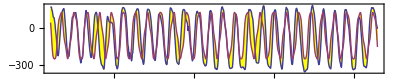

```mathematica
YEARS = 61.25;
Q = MeanFilter[QBO[[All,2]],3];  
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*MONTHS+1, 1}];        
(* Empirical Model fit *)
QBOyear[x_] := -(1.13*Cos[2*Pi/2.3333*x-0.23*Cos[2*Pi*x-0.4]+0.5*Cos[2*Pi/18.63*x+0.9]-1.3] +
                0*0.67*Cos[2*Pi/2.239*x-1.1]);
QBOfit[x_] := QBOyear[x-0.0];
QBOshift[x_] := QBOfit[x*1.00011] ;
QBOM = Table[{1953.0+x, (-200*QBOshift[73.0+x]-72.4)/1.2},{x,1/12,YEARS+1/12, 1/12}];  

SDIF = QBOT[[All,2]]-QBOM[[All,2]];  
OldCC = NewCC; NewCC = 100*Correlation[QBOT,QBOM][[2,2]];  
Var = Variance[SOIT]-Variance[SOIM];
Print[{ "=err" Var[[2]]," 1953 .. 2013 ","CC",OldCC,NewCC,NewCC-OldCC}]

ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, 
             Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}, AspectRatio->0.1]
```

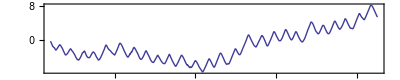

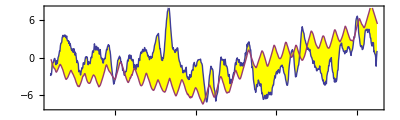

{0.,4.84793}

{7.20731 = char t,4.84793 =err,1953.  .. ,2013.75,CC,18.3607,17.0413,-1.3194}

```mathematica
STRT=876; STRTY=1880+STRT/12; LNGTH=1605; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
MONTHS = 61;
Q = MeanFilter[QBO[[All,2]],0]-0*MeanFilter[QBO[[All,2]],40];  
QQ := Accumulate[Q];
QBOT = Table[{QBOM[[i,1]], (-N[QQ[[i]]]/500.0-i/7.7)/2},{i,1,12*MONTHS-2, 1}]  ;    
ListLinePlot[{QBOT}, AspectRatio->0.2, Frame->True, Axes->False, PlotLegends->{"QBO"}, AspectRatio->0.1]
Window = 7;  SEP=0;
R1 = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
lhs=Table[{1880.0+x,  12*12*(2*R1[[x*12]]-R1[[x*12+1]]-R1[[x*12-1]])-3.4*R1[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  If[x>116.2,-1,1]*QBOshift[x-0.5]*2},{x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,QBOT},PlotRange->{-8,8+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"BabyD","QBOT"},AspectRatio->0.3]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,QBOT][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs]
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
```

{7.30405 = char t,0.0685773 =err,1881.  .. ,1980.,CC,88.0491,56.9509,-31.0982}

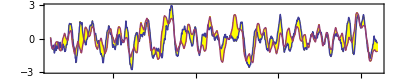

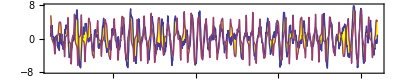

{7.30405 = char t,0.0913204 =err,1881.  .. ,1980.,CC,37.5388,35.3263,-2.21256}

```mathematica
STRT=12; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 7;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.74;  TR=52.0;  SHFT=1.1;
DIU := 18.61;   CWR := 6.4827;  SEMI := 8.85; 
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Diurnal[x_] := -1.49*(0.06*Cos[2*Pi/(DIU/2)*x+3.6] -0.2*Cos[2*Pi/(DIU)*x+2.1] );
Semidiurnal[x_] := 0.17*Cos[2*Pi*x/(SEMI)+0.1]-0.14*Cos[2*Pi*x/(SEMI/2)+0.1];
Others[x_]:= + 2.5*CWG[x-0.4]+1.6*Diurnal[x+2.0]+0.5*Semidiurnal[x-0.3]+0.34*Cos[2*Pi/18.06*x-1.0];  (* RHS[x_] :=(1.25*QBOG[x+0.088]+1.4*CWG[x+0.08]+0.51*Diurnal[x+2.5]+0.9*Semidiurnal[x+0.5] ; *)
RHS[x_] := (-2.0*QBOfit'[x+0.09] + (0.78*QBOfit[x+0.12]) + Others[x] - 0.2*Cos[2*Pi/46.0*x+0.6]+0*1*Cos[2*Pi/2.9*x+0.5])*(1+0.12*Cos[2*Pi/10.6*x+0.8]) -
           0.0*Cos[2*Pi*x-2.5];
SOLN=NDSolve[{y''[x]+CF*y[x] == 1.7*RHS[x-0.0], y'[TR]==-1.2, y[TR]==-0.7}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.4*(0.0*RHS[x+SHFT]-First[y[1.0014*x-0.08*Cos[2*Pi*x-0.6]-0.3*Sin[2*Pi/18.6*x-0.6]+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},   PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
Window = 6;  SEP=0;
R1 = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
lhs=Table[{1880.0+x,  12*12*(2*R1[[x*12]]-R1[[x*12+1]]-R1[[x*12-1]])-0.78*R1[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  -If[x>116.2,-1,1]*RHS[x*1.0012-0.14*Cos[2*Pi*x-0.6]-1.24]/1.52},{x,STRT/12,LNGTH/12+0, 1/12}];    
(* rhs=Table[{1880.0+x,  If[x>116.2,-1,1]*QBOshift[x-0.5]*2},{x,STRT/12,LNGTH/12+0, 1/12}];    *)
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
ListLinePlot[{lhs,rhs},PlotRange->{-8,8+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},    PlotLegends->{"Differential","RHS"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
(* SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,250,1000,250}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
2*Pi/.18/12
```

{7.23593 = char t,-0.0875002 =err,1881.  .. ,1980.,CC,77.2811,72.5352,-4.74583}

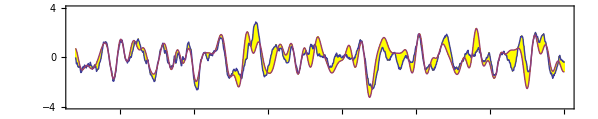

```mathematica
(* First 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.754;  TR=52.0;  SHFT=0.67;
RHS[x_] := 2.2*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.02], y'[TR]==-0.03, y[TR]==0.32}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.8*(-0.109*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

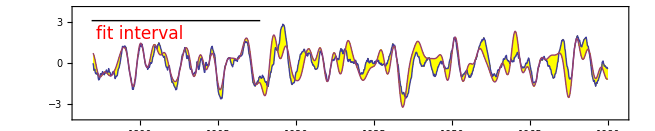

{7.23113 = char t,0.0568367 =err,1946.67  .. ,1980.,CC,70.9426,71.1927,0.250044}

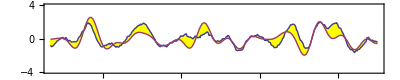

```mathematica
(* Third 400 months *)
STRT=800; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.755;  TR=52.0;  SHFT=0.59;
RHS[x_] := 2.2*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.02], y'[TR]==0.52, y[TR]==0.53}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.9*(-0.122*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

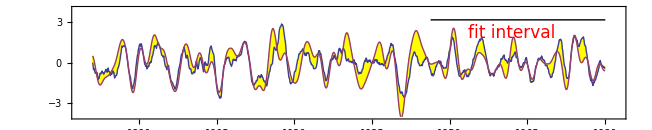

```mathematica
(* Second 400 months *)
STRT=1; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.76;  TR=52.0;  SHFT=0.64;
RHS[x_] := 2.2*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.02], y'[TR]==-0.07, y[TR]==0.1}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.7*(-0.13*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{7.20731 = char t,0.186214 =err,1880.08  .. ,1980.,CC,71.5551,71.5551,0.}

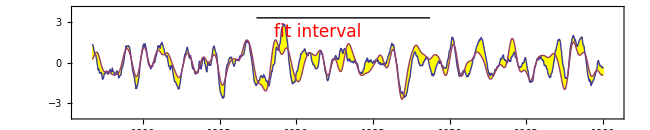

{7.20731 = char t,0.113443 =err,1988.33  .. ,2013.33,CC,47.0414,50.5429,3.50148}

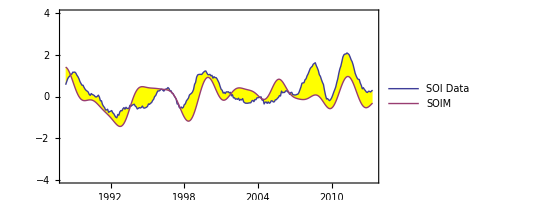

```mathematica
(* Fourth 400 months *)
STRT=1300; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (0*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.76;  TR=52.0;  SHFT=0.7;
RHS[x_] := 7.2*QBOfit[x-0.01]*(1.0 + 0.2*Sin[2*Pi/11.01*x-2.7]);
SOLN=NDSolve[{y''[x]+CF*y[x] +0.0*y'[x] == RHS[x-0.01], y'[TR]==-0.5, y[TR]==-1.8}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.2*(-0.14*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.5]
```

{7.23113 = char t,0.0551895 =err,1996.67  .. ,2013.33,CC,9.97695,9.97695,-3.55271×10^-15}

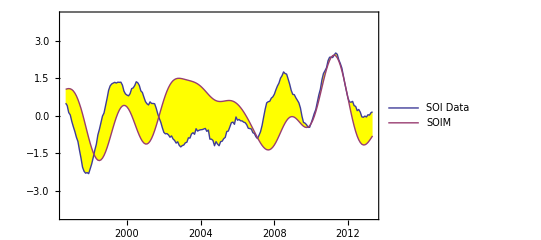

```mathematica
(* Third 400 months *)
STRT=1400; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.755;  TR=52.0;  SHFT=0.59;
RHS[x_] := 2.2*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.02], y'[TR]==0.52, y[TR]==0.53}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.9*(-0.122*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.6]
```

{4.25551 = char t,-1.1049 =err,1980.  .. ,2013.33,CC,8.78982,9.07504,0.285225}

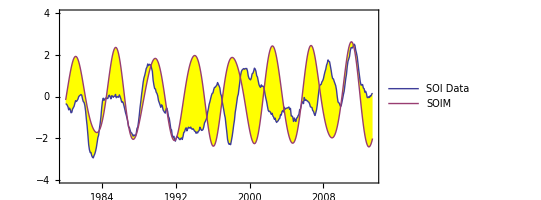

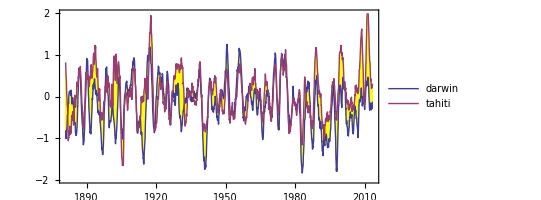

```mathematica
(* Third 400 months *)
STRT=1200; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 2.18;  TR=52.0;  SHFT=0.59;
RHS[x_] := 0.2*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.02], y'[TR]==2.7, y[TR]==0.53}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.9*(-0*0.12*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.5]
R1 = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(0*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
R2 = (0*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT1 = Table[{1880+i/12, -R1[[i]]},{i,12,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
SOIT2 = Table[{1880+i/12, -R2[[i]]},{i,12,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
ListLinePlot[{SOIT1,SOIT2},PlotRange->{-2,2+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"darwin","tahiti"},AspectRatio->0.5]
```

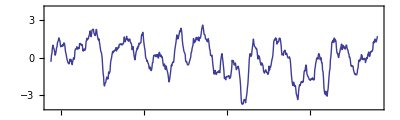

{7.20731 = char t,1.03531 =err,1948.  .. ,2007.17,CC,40.0382,34.9821,-5.05614}

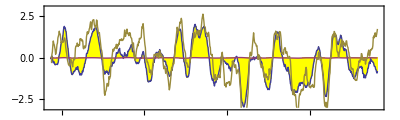

2007.17

```mathematica
R = (1*MeanFilter[noi[[All,2]],WinHiFilter]); 
NOIT = Table[{1948+i/12, R[[i]]},{i,1,710,1}];        (* scaled SOI Data Table from NCAR *)
ListLinePlot[{NOIT},PlotRange->{-4,4},Frame->True,Axes->False, PlotLegends->{"noi"},AspectRatio->0.3]

STRT=816; STRTY=1880+STRT/12; LNGTH=1526; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.76;  TR=52.0;  SHFT=0.7;
RHS[x_] := 7.2*QBOfit[x-0.01]*(1.0 + 0.2*Sin[2*Pi/11.01*x-2.7]);
SOLN=NDSolve[{y''[x]+CF*y[x] +0.0*y'[x] == RHS[x-0.01], y'[TR]==-0.5, y[TR]==-1.8}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.002*(-0.14*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM, NOIT},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM", "NOIT"},AspectRatio->0.3]
710.0/12.0+1948
```

7.96348

{char t,7.2552,-0.353076, Years from,1881.,to,2013.33,CC,66.1758,66.0325,-0.143221}

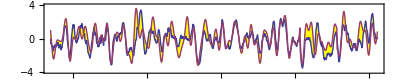

```mathematica
(* Third 1/4 -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=12; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1600; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.75;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.05*Cos[2*Pi/OSC*x+3.6] -0.1*Cos[2*Pi/(2*OSC)*x+1.7] - 0.12*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.02*Cos[2*Pi*x/(SEMI)-0.2]-0.14*Cos[2*Pi*x/(SEMI/2)-0.6];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(1.25*QBOG[x+0.088]+1.38*QTO[x-0.36])+1.4*CWG[x+0.08]+0.51*Diurnal[x+2.5]+0.9*Semidiurnal[x+0.5] ;
(* This has drag coefficient, an extra Mathieu modulation, and DiracDelta *)
SOLN=NDSolve[{y''[x]+CF*y[x]*(1+0.075*Sin[2*Pi/8.0*(x-0.7)])+0.02*y'[x] == 0.93*RHS[x-0.02]- 0*.3*DiracDelta[x-104.5] - 0.92*DiracDelta[x-111.5],  (* ElChicon 102.33, Pinatubo 111.5 *)
              y'[TR]==0.18, y[TR]==0.25}, y, {x, 0, 260}]; 
(* SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]-First[2.2*y[x+0.63] /. SOLN]},        {x,STRT/12,LNGTH/12+0, 1/12}];    *)
SOIM=Table[{1880.0+x, If[x>102.0&&x<117, -1, 1]* (-0.27*QBOG[x+0.68]-First[2.2*y[x+0.63] /. SOLN])  },        {x,STRT/12,LNGTH/12+0, 1/12}];   
2*Pi/0.789
(* x>101&&x<115 *)
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

```mathematica
CWTT=ContinuousWaveletTransform[SOIT[[All,2]]];  Print[{"SOI Data"}]
WaveletScalogram[CWTT, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}} ]
CWTM=ContinuousWaveletTransform[SOIM[[All,2]]];  Print[{"SOI Model"}]
WaveletScalogram[CWTM, Frame->True, AspectRatio->0.3, FrameTicks->{{1,2,3,4,5,6,7,8,9},{{{0,1880},{240,1900},{480,1920},{720,1940},{960,1960},{1200,1980},{1440,2000}},None}}]
```

{SOI Data}

-Graphics-

{SOI Model}

-Graphics-

7.96348

{char t,7.2552,-0.478878, Years from,1881.,to,2013.33,CC,65.5468,65.5495,0.00267799}

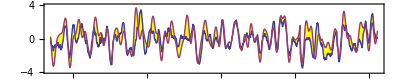

```mathematica
(* Third 1/4 -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=12; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1600; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.75;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.05*Cos[2*Pi/OSC*x+3.6] -0.1*Cos[2*Pi/(2*OSC)*x+1.7] - 0.12*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.02*Cos[2*Pi*x/(SEMI)-0.2]-0.14*Cos[2*Pi*x/(SEMI/2)-0.6];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(1.25*QBOG[x+0.088]+1.38*QTO[x-0.36])+1.4*CWG[x+0.08]+0.51*Diurnal[x+2.5]+0.9*Semidiurnal[x+0.5] ;
(* This has drag coefficient, an extra Mathieu modulation, and DiracDelta *)
SOLN=NDSolve[{y''[x]+CF*y[x]*(1-0.022*RHS[x])+0.02*y'[x] == 0.93*RHS[x-0.02]- 0*.3*DiracDelta[x-104.5] - 0.92*DiracDelta[x-111.5],  (* ElChicon 102.33, Pinatubo 111.5 *)
              y'[TR]==0.18, y[TR]==0.25}, y, {x, 0, 260}]; 
(* SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]-First[2.2*y[x+0.63] /. SOLN]},        {x,STRT/12,LNGTH/12+0, 1/12}];    *)
SOIM=Table[{1880.0+x, If[x>102.0&&x<117, -1, 1]* (-0.27*QBOG[x+0.68]-First[2.2*y[x+0.63] /. SOLN])  },        {x,STRT/12,LNGTH/12+0, 1/12}];   
2*Pi/0.789
(* x>101&&x<115 *)
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{7.23593 = char t,-0.0875002 =err,1881.  .. ,1980.,CC,53.8924,72.5352,18.6428}

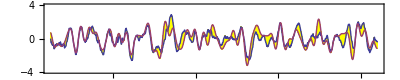

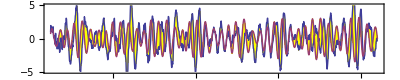

```mathematica
(* First 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
Window = 7;  SEP=0;
R1 = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.754;  TR=52.0;  SHFT=0.67;
RHS[x_] := 2.2*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.02], y'[TR]==-0.03, y[TR]==0.32}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.8*(-0.109*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
lhs=Table[{1880.0+x,  12*12*(2*R1[[x*12]]-R1[[x*12+1]]-R1[[x*12-1]])-CF*R1[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  RHS[x]/6},{x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"BabyD","QBOM"},AspectRatio->0.2]
```

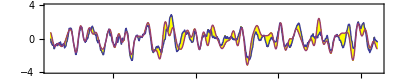

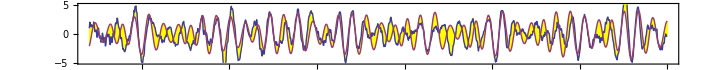

{0.,0.17317}

{7.23593 = char t,0.17317 =err,1881.  .. ,1980.,CC,53.8663,53.8924,0.0260742}

```mathematica
(* First 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
Window = 7;  SEP=0;
R1 = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.754;  TR=52.0;  SHFT=0.67;
RHS[x_] := 2.2*QBOfit[x-0.000012*x*x+0.02];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.02], y'[TR]==-0.03, y[TR]==0.32}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.8*(-0.109*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
lhs=Table[{1880.0+x,  12*12*(2*R1[[x*12]]-R1[[x*12+1]]-R1[[x*12-1]])-0.93*(1+0.5*Sin[2*Pi/10.11*x-2.6])*R1[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  (RHS[x-0.6]+0.0*RHS[x-0.0])/4.75},{x,STRT/12,LNGTH/12+0, 1/12}];    
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"BabyD","QBOM"},AspectRatio->0.1]
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs]
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
```

{-0.0826836 =err,1881.  .. ,1980.,CC,11.273,77.2811,66.0081}

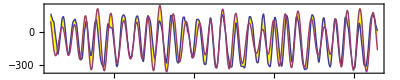

```mathematica
(* Data *)
MONTHS = 61.25;
Q = MeanFilter[QBO[[All,2]],4];  
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*MONTHS+1, 1}];        
(* Empirical Model fit *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
OSC := 9.305;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.036*Cos[2*Pi*x/(SEMI)+0.45]-0.17*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 
                     0.071*Cos[2*Pi*x/(CWR)+2.0]];
QBOfit[x_] :=(1.3*QBOG[x+0.0889]+1.2*QTO[x+0.0889])+1.16*CWG[x-0.04]+0.58*Diurnal[x+2.1]+1.23*Semidiurnal[x+0.6] ;
QBOshift[x_] := QBOfit[x-0.000012*x*x-0.31] ;
QBOM = Table[{1953.0+x, (-34.17*QBOshift[73.0+x]-72.4)/1},{x,1/12,MONTHS+1/12, 1/12}];  

SDIF = QBOT[[All,2]]-QBOM[[All,2]];  
OldCC = NewCC; NewCC = 100*Correlation[QBOT,QBOM][[2,2]];  
Var = Variance[SOIT]-Variance[SOIM];
Print[{ "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]

ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}, AspectRatio->0.1]
```

{-0.0875002 =err,1881.  .. ,1980.,CC,72.5352,87.0864,14.5512}

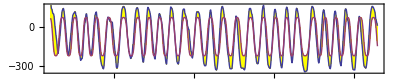

```mathematica
(* 234.320138688348*sin(1.47908160811451*cos(2.667874651*year + sin(2.56185156975765 + sin(0.2056357009*year) - sin(0.1697012411*year + sin(0.2056357009*year)*sin(0.0652446035803808*year)) - 0.365511588088449*year))) - 84.5168690958165 *)
(* Data *)
MONTHS = 61.25;
Q = MeanFilter[QBO[[All,2]],4];  
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*MONTHS+1, 1}];        
(* Empirical Model fit *)

QBOyear[x_] := -Sin[1.47908160811451*Cos[2.667874651*x + Sin[2.56185156975765 + Sin[0.2056357009*x] - Sin[0.1697012411*x + 
               Sin[0.2056357009*x]*Sin[0.0652446035803808*x]] - 0.365511588088449*x]]] ;
QBOfit[x_] := QBOyear[x+1880.0-0.2] ;
QBOshift[x_] := QBOfit[x] ;
QBOM = Table[{1953.0+x, (-150*QBOshift[73.0+x]-72.4)/1},{x,1/12,MONTHS+1/12, 1/12}];  

SDIF = QBOT[[All,2]]-QBOM[[All,2]];  
OldCC = NewCC; NewCC = 100*Correlation[QBOT,QBOM][[2,2]];  
Var = Variance[SOIT]-Variance[SOIM];
Print[{ "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]

ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}, AspectRatio->0.1]
```

{6.58657 = char t,0.0424814 =err,1881.  .. ,1980.,CC,69.4874,69.4874,0.}

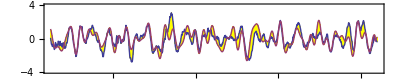

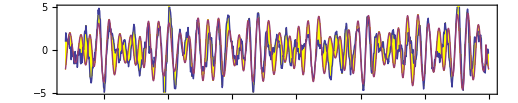

{0.,-0.229322}

{6.58657 = char t,-0.229322 =err,1881.  .. ,1980.,CC,52.8721,52.9918,0.119742}

```mathematica
(* First 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 7;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
Window = 7;  SEP=0;
R1 = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.754;  TR=52.0;  SHFT=0.71;
CF = 0.91;
RHS[x_] := 2.2*QBOfit[x];
RHS[x_] := 2.2*QBOshift[x+0.32];
Hill[x_] := CF*(1+0.26*Sin[2*Pi/9.94*x-4.0]);
SOLN=NDSolve[{y''[x]+Hill[x]*y[x]+0.012*y'[x] == 2.4*RHS[x-0.05]+ 0*.4*DiracDelta[x-101.3] - 3.8*DiracDelta[x-111.8]+3.3*DiracDelta[x-114], 
                  y'[TR]==2.0, y[TR]==2.8}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, If[x>99.3&&x<116.3,-1,1]*0.26*(-0.2*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
lhs=Table[{1880.0+x,  12*12*(2*R1[[x*12]]-R1[[x*12+1]]-R1[[x*12-1]])-Hill[x*12]*R1[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  If[x>99.3&&x<116.3,-1,1]*RHS[x-0.61]/4.5},{x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
ListLinePlot[{lhs,rhs},PlotRange->{-5,5+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"BabyD","QBOM"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs]
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
```

{7.18842 = char t,0.329598 =err,1881.  .. ,2013.33,CC,14.9625,44.8634,29.9009}

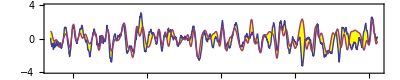

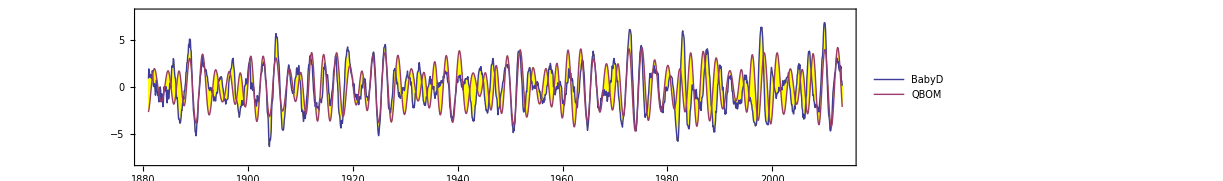

{0.,0.396086}

{7.18842 = char t,0.396086 =err,1881.  .. ,2013.33,CC,19.6053,37.1716,17.5663}

```mathematica
(* First 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 7;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
Window = 7;  SEP=0;
R1 = MeanFilter[MeanFilter[(1*MeanFilter[darwin[[All,2]],Window])-(1*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.754;  TR=52.0;  SHFT=0.69;
CF = 0.764;
RHS[x_] := 2.2*QBOfit[x];
RHS[x_] := 2.2*QBOshift[x+0.32];
Hill[x_] := CF*(1+0.0*Sin[2*Pi/9.06*x-3.0]+0.0*Sin[2*Pi/6.3*x-2.3]);
SOLN=NDSolve[{y''[x]+Hill[x]*y[x]+0.012*y'[x] == 2.2*RHS[x-0.05]+ 0*(3.2*DiracDelta[x-102.4] - 0.0*DiracDelta[x-111.8]+2.5*DiracDelta[x-114.5]), 
                  y'[TR]==1.1, y[TR]==0.8}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, If[x>99.3&&x<116.3,1,1]*0.3*(-0.24*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
lhs=Table[{1880.0+x,  12*12*(2*R1[[x*12]]-R1[[x*12+1]]-R1[[x*12-1]])-Hill[x*12]*R1[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  If[x>99.3&&x<116.3,1,1]*RHS[x-0.58]/4.5},{x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
ListLinePlot[{lhs,rhs},PlotRange->{-8,8+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"BabyD","QBOM"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs]
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
```

{6.62306 = char t,0.0989953 =err,1983.83  .. ,2013.33,CC,54.9468,54.9468,0.}

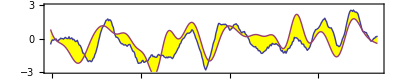

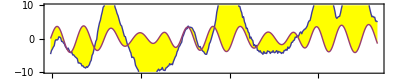

{0.,87.585}

{6.62306 = char t,87.585 =err,1983.83  .. ,2013.33,CC,14.0371,-7.3626,-21.3997}

```mathematica
(* Note that tahiti is important and Darwin not so much *)
STRT=1246; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 7;  
R = (1.0*MeanFilter[darwin[[All,2]],WinHiFilter])-(1.0*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
Window = 7;  SEP=0;
R1 = MeanFilter[MeanFilter[(0.1*MeanFilter[darwin[[All,2]],Window])-(1.4*MeanFilter[tahiti[[All,2]],Window]),Window-2],Window-4];
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.754;  TR=102.0;  SHFT=0.48;
CF = 0.9;
RHS[x_] := 2.2*QBOfit[x];
RHS[x_] := 2.2*QBOshift[x+0.32];
Hill[x_] := CF*(1-0.13*Sin[2*Pi/9.06*x-2.5]+0.19*Sin[2*Pi/6.3*x-2.4]) + 0.008*(x-100);
SOLN=NDSolve[{y''[x]+Hill[x]*y[x]+0.03*y'[x] == 1.6*RHS[x+0.07]+ 1*(-0.0*DiracDelta[x-103.0] - 0.0*DiracDelta[x-111.8]+0*2.5*DiracDelta[x-114.5]), 
                  y'[TR]==-0.6, y[TR]==-0.2}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, If[x>99.3&&x<116.3,1,1]*0.7*(-0.27*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
lhs=Table[{1880.0+x,  12*12*(2*R1[[x*12]]-R1[[x*12+1]]-R1[[x*12-1]])-Hill[x*12]*R1[[x*12]]},{x,STRT/12,LNGTH/12+0, 1/12}];    
rhs=Table[{1880.0+x,  If[x>99.3&&x<116.3,1,1]*RHS[x-0.58]/4.5},{x,STRT/12,LNGTH/12+0, 1/12}];    
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-3,3+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"BabyD","QBOM"},AspectRatio->0.2]
OldCC1 = NewCC1; NewCC1 = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Var = Variance[lhs]-Variance[rhs]
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
```

{7.19312 = char t,-0.0504794 =err,1881.  .. ,1980.,CC,74.2118,74.2318,0.0200058}

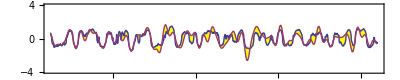

```mathematica
(* Third 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (0.4*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -Sign[R[[i]]]*Sqrt[Abs[R[[i]]]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.763;  TR=52.0;  SHFT=0.66;
RHS[x_] := 2.7*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.013], y'[TR]==0.32, y[TR]==0.39}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.5*(-0.12*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{7.20257 = char t,0.1932 =err,1881.  .. ,2013.33,CC,62.6841,62.714,0.0298233}

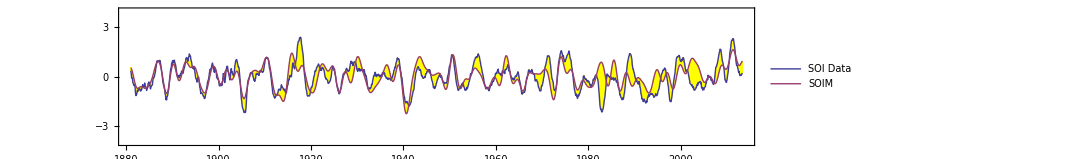

```mathematica
(* Third 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (0.55*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.761;  TR=52.0;  SHFT=0.61;   PCS:= 100.0;
RHS[x_] := 2.9*QBOfit[x];
Hill[x_] := CF*(1-HeavisideTheta[x-PCS]*1.0*Sin[0.623*(x-PCS)+0.99]);
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x-0.01], y'[TR]==0.27, y[TR]==0.32}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.4*(-0.12*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{6.8719 = char t,-1.71714 =err,1881.  .. ,2013.33,CC,57.0478,43.3818,-13.6659}

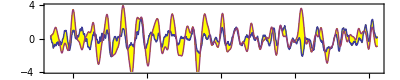

```mathematica
(* Third 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (0.55*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.836;  TR=52.0;  SHFT=0.65;   PCS:= 100.0;
RHS[x_] := 4.5*QBOfit[x];
Hill[x_] := CF*(1-HeavisideTheta[x-PCS]*0.98*Sin[0.621*(x-PCS)+0.98]);
Hill[x_] := CF*(1-HeavisideTheta[x-PCS]*0.64*Sin[1.0*(x-PCS)-0.7]);
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == RHS[x+0.01], y'[TR]==1.4, y[TR]==-1.8}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.45*(-0.14*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

```mathematica
(* 1.43291061172553*sin(2.69422811429272*Time)+sin(2.62913771202866*Time)+sin(2.59174459165929*Time)-cos(-2.97859233185186*Time) *)
```

{7.23113 = char t,0.555349 =err,1881.  .. ,1980.,CC,0.382537,0.382537,-1.22125×10^-15}

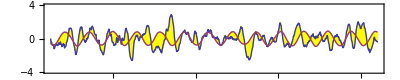

```mathematica
STRT=12; STRTY=1880+STRT/12; LNGTH=1200; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.755;  TR=52.0;  SHFT=0.59;
QBObeat[x_] := 1.43291*Sin[2.6942281*x] + Sin[2.62913771*x] + Sin[2.59174*x] - Cos[-2.978592*x];
RHS[x_] := -0.1*QBOfit[x+1.0];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.02], y'[TR]==0.52, y[TR]==0.53}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.9*(-0.122*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{7.17434 = char t,-0.893687 =err,1881.  .. ,2013.33,CC,14.0536,14.0536,0.}

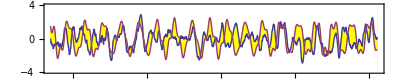

{7.17434 = char t,15994.6 =err,1881.  .. ,2013.33,CC,6.43873,-36.7463,-43.1851}

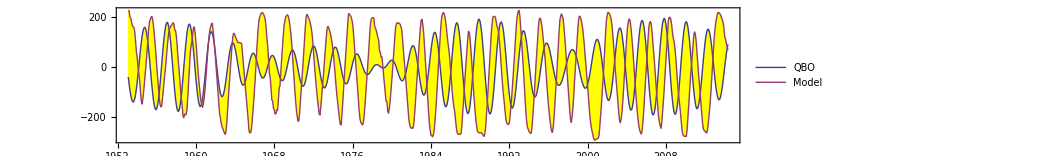

```mathematica
(* Third 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.767;  TR=52.0;  SHFT=5.95; ST:=+0.51;
QBObeat[x_] := 1.43291*Sin[2.6942281*x+ST] + Sin[2.62913771*x+ST] + Sin[2.59174*x+ST] - Cos[-2.978592*x+ST];
RHS[x_] := 2.3*QBObeat[x+0.9];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x+0.4], y'[TR]==+0.1, y[TR]==+0.4}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.7*(-0*0.122*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]

MONTHS = 61.25;
Q = MeanFilter[QBO[[All,2]],4];  
QBOT = Table[{QBOM[[i,1]], Q[[i]]+54},{i,1,12*MONTHS+1, 1}];        
QBOM = Table[{1953.0+x, 70.17*QBObeat[x+20.21]},{x,1/12,MONTHS+1/12, 1/12}];  
OldCC1 = NewCC1; NewCC1 = 100*Correlation[QBOT,QBOM][[2,2]];  Var = Variance[QBOT]-Variance[QBOM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC1,NewCC1,NewCC1-OldCC1}]
ListLinePlot[{QBOM, QBOT}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}, AspectRatio->0.1]
```

{7.23113 = char t,-0.180077 =err,1995.83  .. ,2013.33,CC,52.0935,52.0849,-0.0086196}

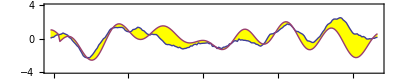

```mathematica
(* Third 400 months *)
STRT=1390; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.755;  TR=52.0;  SHFT=0.99;
RHS[x_] := 1.7*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*y[x] == RHS[x-0.14], y'[TR]==2.2, y[TR]==1.8}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.58*If[x>99.3&&x<116.3,-1,1]*(+0.01*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{7.23113 = char t,0.707001 =err,1984.67  .. ,2013.33,CC,33.6192,32.3757,-1.24355}

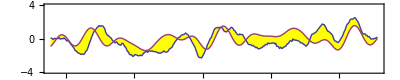

```mathematica
(* Third 400 months *)
STRT=1256; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.755;  TR=52.0;  SHFT=0.59;  PCS:=99.9;
RHS[x_] := 2.2*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*(1+0.6*HeavisideTheta[x-PCS]*Sin[2*Pi/1*(x-PCS)]*Exp[-(x-PCS)/0.5])*y[x] == 
             RHS[x-0.02] + 0.5*(HeavisideTheta[x-98.3]-HeavisideTheta[x-102.4]),  y'[TR]==0.52, y[TR]==0.53}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.9*(-0.122*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{7.23113 = char t,-0.00326456 =err,1881.  .. ,2013.33,CC,66.0459,66.1046,0.0586964}

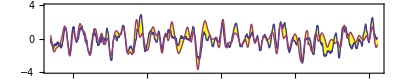

```mathematica
(* Third 400 months *)
STRT=12; STRTY=1880+STRT/12; LNGTH=1600; ENDY=1880+LNGTH/12;  WinHiFilter = 8;  
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
SOIT = Table[{1880+i/12, -R[[i]]},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.755;  TR=52.0;  SHFT=0.59;  PCS:=101.0;
RHS[x_] := 2.2*QBOfit[x];
SOLN=NDSolve[{y''[x]+CF*(1-0.0*HeavisideTheta[x-PCS]*Cos[2*Pi/6.5*(x-PCS)]*Exp[-0*(x-PCS)/0.5])*y[x] == RHS[x-0.02]*(1-0.08*HeavisideTheta[x-PCS]) -
              0.42*(HeavisideTheta[x-PCS]*Sin[2*Pi/9.0*(x-PCS)]-0.01)*Exp[-(x-PCS)/32],  
             y'[TR]==0.52, y[TR]==0.53}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, 0.82*If[x>99.3&&x<105.2,-1,1]*(-0.122*RHS[x+SHFT]-First[y[x+SHFT] /. SOLN])},{x, STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"= char t" 2*Pi/Sqrt[CF], "=err" Var[[2]]," .. " N[STRTY], N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  
              PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```